```mathematica
data=Import["D:\\Mod\\temperature.xlsx"];(*从文件中读取数据*)
```

```mathematica
TemperatureCurve=Table[{data[[1]][[i]][[1]],data[[1]][[i]][[2]]},{i,3,5403}];(*抓取温度-时间数据*)
```

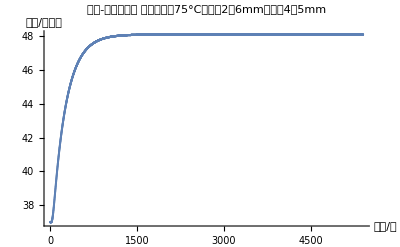

```mathematica
ListPlot[TemperatureCurve,PlotRange->All,PlotLabel->"温度-时间曲线图
环境温度：75°C，厚度2：6mm，厚度4：5mm",AxesLabel->{"时间/秒","温度/摄氏度"}]
```

```mathematica
(*绘制温度-时间曲线*)
```